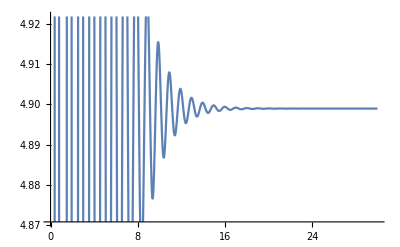

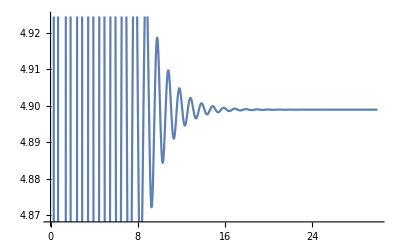

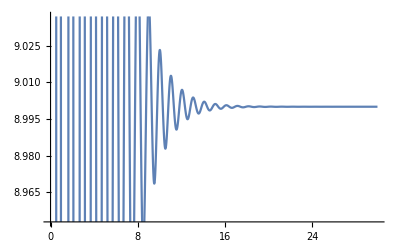

-Graphics3D-

```mathematica
tend=30;
eq={x'[t]==σ (y[t]-x[t]),y'[t]==x[t] (ρ-z[t])-y[t],z'[t]==x[t] y[t]-β z[t]};
init={x[0]==1,y[0]==1,z[0]==1};
pars={σ->10,ρ->10,β->8/3};
{xs,ys,zs}=NDSolveValue[{eq/.pars,init},{x,y,z},{t,0,tend}];
Plot[xs[t],{t,0,tend}]
Plot[ys[t],{t,0,tend}]
Plot[zs[t],{t,0,tend}]
ParametricPlot3D[{xs[t],ys[t],zs[t]},{t,0,tend}]
```

```mathematica
eq={x'[t]==σ (y[t]-x[t]),y'[t]==x[t] (ρ-z[t])-y[t],z'[t]==x[t] y[t]-β z[t]};
init={x[0]==1,y[0]==1,z[0]==1};
pars={σ->10,ρ->15,β->8/3};
{xs,ys,zs}=NDSolveValue[{eq/.pars,init},{x,y,z},{t,0,tend}];
{xs[30],ys[30],zs[30]}
init={x[0]==2,y[0]==2,z[0]==2};
{xs,ys,zs}=NDSolveValue[{eq/.pars,init},{x,y,z},{t,0,tend}];
{xs[30],ys[30],zs[30]}
init={x[0]==0.5,y[0]==0.5,z[0]==2};
{xs,ys,zs}=NDSolveValue[{eq/.pars,init},{x,y,z},{t,0,tend}];
{xs[30],ys[30],zs[30]}
```

{-6.10969,-6.10963,13.9997}

{6.10981,6.11002,13.9994}

{-6.10965,-6.10911,14.0005}

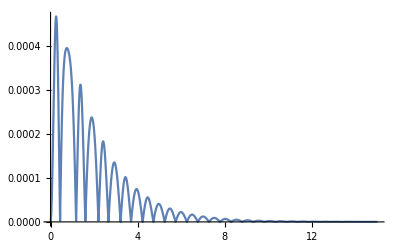

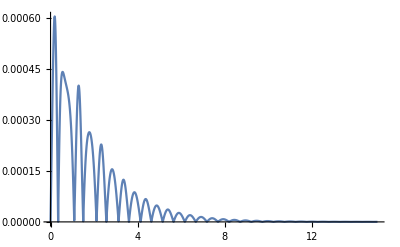

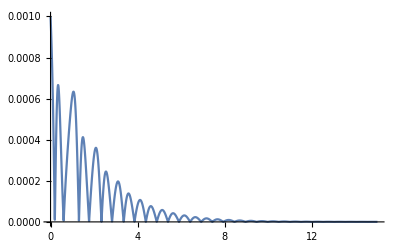

-Graphics3D-

```mathematica
eq={x'[t]==σ (y[t]-x[t]),y'[t]==x[t] (ρ-z[t])-y[t],z'[t]==x[t] y[t]-β z[t]};
init={x[0]==4,y[0]==6,z[0]==5};
pars={σ->10,ρ->10,β->8/3};
{xs,ys,zs}=NDSolveValue[{eq/.pars,init},{x,y,z},{t,0,tend}];
init={x[0]==4,y[0]==6,z[0]==5.001};
{x2s,y2s,z2s}=NDSolveValue[{eq/.pars,init},{x,y,z},{t,0,tend}];
Plot[Abs[xs[t]-x2s[t]],{t,0,15},PlotRange->All]
Plot[Abs[ys[t]-y2s[t]],{t,0,15},PlotRange->All]
Plot[Abs[zs[t]-z2s[t]],{t,0,15},PlotRange->All]
ParametricPlot3D[{{x2s[t],y2s[t],z2s[t]},{xs[t],ys[t],zs[t]}},{t,0,tend}]
```

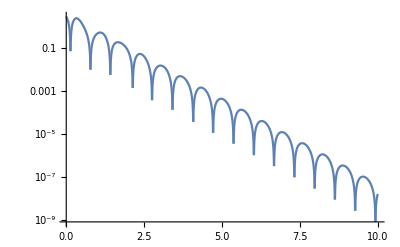

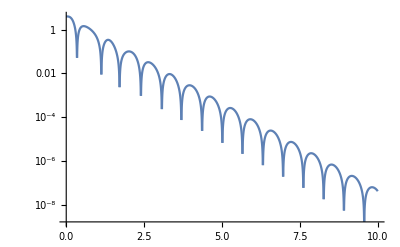

-Graphics3D-

```mathematica
tend=30;
eq={x'[t]==σ (y[t]-x[t]),y'[t]==x[t] (ρ-z[t])-y[t],z'[t]==x[t] y[t]-β z[t],xr'[t]==σ(yr[t]-xr[t]),yr'[t]==x[t](ρ-zr[t])-yr[t],zr'[t]==x[t] yr[t]-β zr[t]};
init={x[0]==4,y[0]==6,z[0]==5,xr[0]==10,yr[0]==3,zr[0]==1};
pars={σ->10,ρ->10,β->8/3};
{xs,ys,zs,x2s,y2s,z2s}=NDSolveValue[{eq/.pars,init},{x,y,z,xr,yr,zr},{t,0,tend}];
LogPlot[Abs[ys[t]-y2s[t]],{t,0,10},PlotRange->All]
LogPlot[Abs[zs[t]-z2s[t]],{t,0,10},PlotRange->All]
ParametricPlot3D[{{x2s[t],y2s[t],z2s[t]},{xs[t],ys[t],zs[t]}},{t,0,tend}]
```

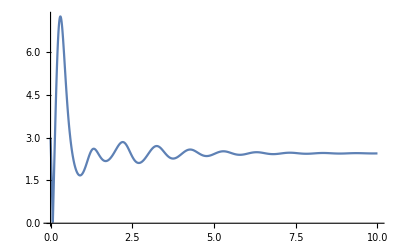

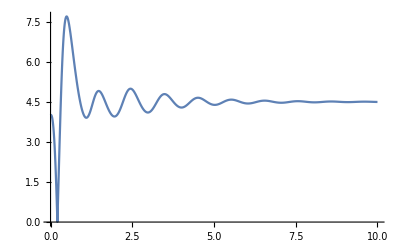

-Graphics3D-

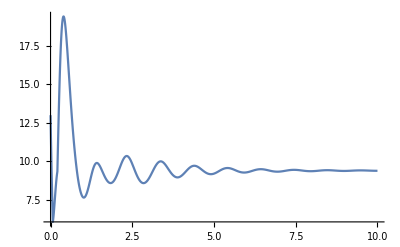

```mathematica
tend=30;
eq={x'[t]==σ (y[t]-x[t]),y'[t]==x[t] (ρ-z[t])-y[t],z'[t]==x[t] y[t]-β z[t],xr'[t]==σ(yr[t]-xr[t]),yr'[t]==x[t](ρr-zr[t])-yr[t],zr'[t]==x[t] yr[t]-β zr[t]};
init={x[0]==4,y[0]==6,z[0]==5,xr[0]==10,yr[0]==3,zr[0]==1};
pars={σ->10,ρ->10,β->8/3,ρr->15};
{xs,ys,zs,x2s,y2s,z2s}=NDSolveValue[{eq/.pars,init},{x,y,z,xr,yr,zr},{t,0,tend}];
Plot[Abs[ys[t]-y2s[t]],{t,0,10},PlotRange->All]
Plot[Abs[zs[t]-z2s[t]],{t,0,10},PlotRange->All]
ParametricPlot3D[{{x2s[t],y2s[t],z2s[t]},{xs[t],ys[t],zs[t]}},{t,0,tend}]
Plot[Abs[xs[t]-x2s[t]]+Abs[ys[t]-y2s[t]]+Abs[zs[t]-z2s[t]],{t,0,10},PlotRange->All]
```

```mathematica
encoder[bs_]:=Module[{},
Table[5 bs[[i]]+10,{i,1,Length@bs}]
]
runSys[τ_,ρt_,init_]:=Module[{eq={x'[t]==σ (y[t]-x[t]),y'[t]==x[t] (ρ-z[t])-y[t],z'[t]==x[t] y[t]-β z[t],xr'[t]==σ(yr[t]-xr[t]),yr'[t]==x[t](ρr-zr[t])-yr[t],zr'[t]==x[t] yr[t]-β zr[t]},pars={σ->10,ρ->ρt,β->8/3,ρr->10}},
NDSolveValue[{eq/.pars,init},{x,y,z,xr,yr,zr},{t,0,τ}]
]
transmitter[ρs_,τ_]:=Module[{x0=4,y0=6,z0=5,xr0=10,yr0=3,zr0=1},
Table[{xs,ys,zs,x2s,y2s,z2s}=runSys[τ,ρs[[i]],{x[0]==x0,y[0]==y0,z[0]==z0,xr[0]==xr0,yr[0]==yr0,zr[0]==zr0}];x0=xs[τ];y0=ys[τ];z0=zs[τ];xr0=x2s[τ];yr0=y2s[τ];zr0=z2s[τ];{z0,zr0},{i,1,Length@ρs}]
]
decoder[zs_,th_]:=Module[{},
Table[If[Abs[zs[[i,1]]-zs[[i,2]]]<th,0,1],{i,1,Length@zs}]
]
sendSignal[signal_,τ_,th_]:=decoder[transmitter[encoder[signal],τ],th]
```

```mathematica
signal=Table[RandomInteger[],{i,100}]
sendSignal[signal,30,1]
```

{0,0,1,0,0,0,1,0,1,0,1,0,1,1,1,1,1,1,0,1,1,0,1,1,1,1,0,0,0,1,1,1,1,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,0,0,0,1,1,1,0,0,1,0,0,0,0,0,1,1,1,1,0,1,0,0,1,1,0,1,1,1,0,1,1,1,1,0,1,1,1,0,1,1,0,1,1}

{0,0,1,0,0,0,1,0,1,0,1,0,1,1,1,1,1,1,0,1,1,0,1,1,1,1,0,0,0,1,1,1,1,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,0,0,0,1,1,1,0,0,1,0,0,0,0,0,1,1,1,1,0,1,0,0,1,1,0,1,1,1,0,1,1,1,1,0,1,1,1,0,1,1,0,1,1}

```mathematica
transmitter2[ρs_,τ_]:=Module[{x0=4,y0=6,z0=5,xr0=10,yr0=3,zr0=1},
Table[{xs,ys,zs,x2s,y2s,z2s}=runSys[τ,ρs[[i]],{x[0]==x0,y[0]==y0,z[0]==z0,xr[0]==xr0,yr[0]==yr0,zr[0]==zr0}];x0=xs[τ];y0=ys[τ];z0=zs[τ];xr0=x2s[τ];yr0=y2s[τ];zr0=z2s[τ];{xs,ys,zs,x2s,y2s,z2s},{i,1,Length@ρs}]
]
sample[if_,τ_]:=Module[{},
Table[if[t],{t,0,τ,0.1}]
]
fixData[data_,τ_]:=Table[Flatten[Table[sample[data[[i,j]],τ],{i,Length@data}],1],{j,6}]
```

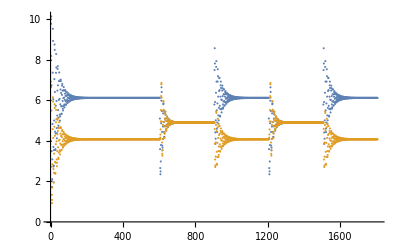

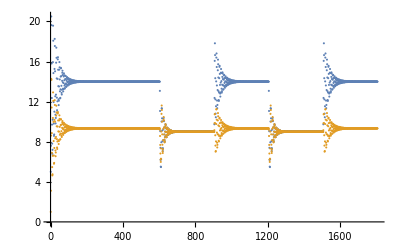

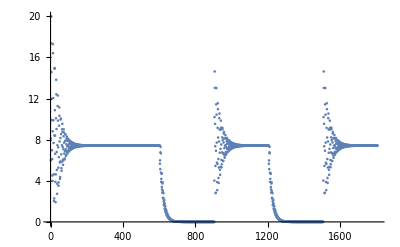

```mathematica
data=transmitter2[encoder[{1,1,0,1,0,1}],30];
{xs,ys,zs,x2s,y2s,z2s}=fixData[data,30];
ListPlot[{xs,x2s}]
ListPlot[{zs,z2s}]
ListPlot[
Table[Abs[xs[[t]]-2 Sqrt[6]]+Abs[ys[[t]]-2 Sqrt[6]]+Abs[zs[[t]]-9],{t,Min[Length@xs,Length@ys,Length@zs]}]]
```

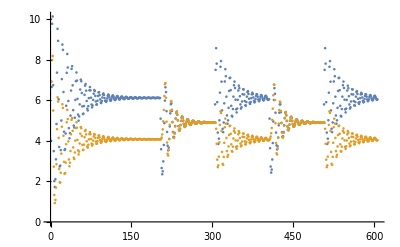

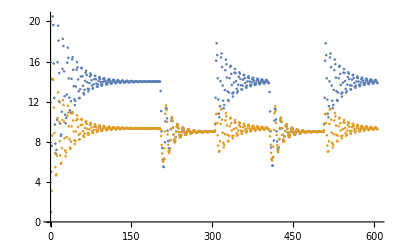

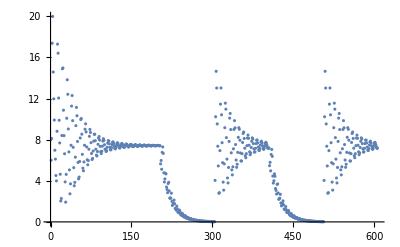

```mathematica
data=transmitter2[encoder[{1,1,0,1,0,1}],10];
{xs,ys,zs,x2s,y2s,z2s}=fixData[data,10];
ListPlot[{xs,x2s}]
ListPlot[{zs,z2s}]
ListPlot[Table[Abs[xs[[t]]-2 Sqrt[6]]+Abs[ys[[t]]-2 Sqrt[6]]+Abs[zs[[t]]-9],{t,Min[Length@xs,Length@ys,Length@zs]}]]
```

{0,1,1,0,0,0,0,0,1,1,1,0,0,0,0,0,1,1,0,1,1,1,1,1,1,0,0,1,0,1,0,1,1,0,1,0,0,1,0,1,1,1,1,1,0,1,0,1,0,0,0,1,0,0,1,1,0,1,1,0,1,1,0,1,0,1,0,1,1,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,1,1,1,1,1,1,1,0,0,1,1,0,0,0,0,1}

{0,1,1,0,0,0,0,0,1,1,1,0,0,0,0,0,1,1,0,1,1,1,1,1,1,0,0,1,0,1,0,1,1,0,1,0,0,1,0,1,1,1,1,1,0,1,0,1,0,0,0,1,0,0,1,1,0,1,1,0,1,1,0,1,0,1,0,1,1,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,1,1,1,1,1,1,1,0,0,1,1,0,0,0,0,1}

0

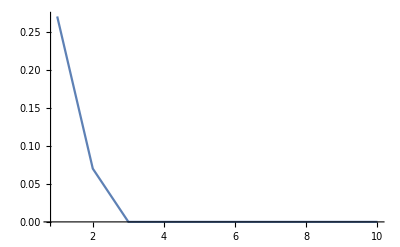

```mathematica
signal=Table[RandomInteger[],{i,100}]
output=sendSignal[signal,10,0.1]
ber[in_,out_]:=Module[{},
1/(Length@in)Length@(Table[If[in[[i]]≠out[[i]],1,0],{i,Length@in}]//DeleteCases[0])
]
ber[signal,output]
ListPlot[Table[ber[signal,sendSignal[signal,i]],{i,1,10}],Joined->True,PlotRange->All]
```

```mathematica
berData=Table[{i,ber[signal,sendSignal[signal,i,0.1]]},{i,1,4,0.01}];
```

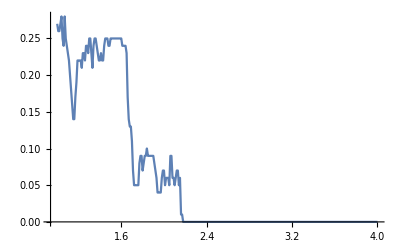

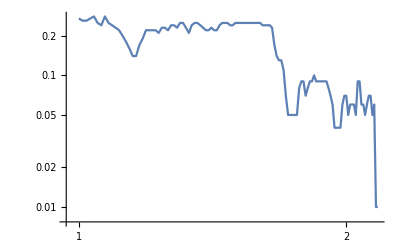

```mathematica
ListPlot[berData,Joined->True]
ListLogLogPlot[berData,Joined->True]
```

```mathematica
berData2=Table[{i,ber[signal,sendSignal[signal,i,j]]},{i,1,3,0.5},{j,1,4}];
```

```mathematica
ListPlot3D[berData2]
```

-Graphics3D-

## Brownian Motion

### Long Time Scale

5.83568×10^-7

-Graphics-

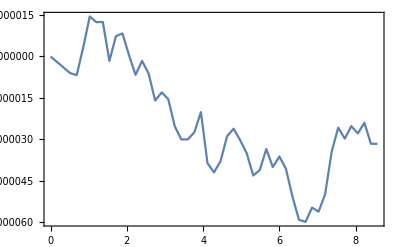

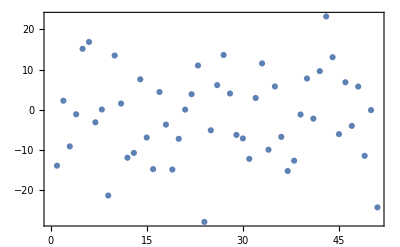

```mathematica
dt=0.01;tend=1.5;
xs=Table[{0,0},{i,1,tend,dt}];
x2s=Table[{0,0},{i,1,tend,dt}];
ws=Table[RandomVariate[NormalDistribution[]]/Sqrt[dt],{i,1,tend,dt}];
m=11 10^-15;γ=6 Pi 0.001 10^-6;temp=300;kb=1.38 10^-23;τ=m/γ
For[t=3,t<tend/dt,t++,
xs[[t]]={t/τ,(2+dt γ/m)/(1+dt γ/m)xs[[t-1,2]]-1/(1+dt γ/m)xs[[t-2,2]]+Sqrt[2 kb temp γ]/(m(1+dt γ/m))dt^(3/2)ws[[t]]};
x2s[[t]]={t/τ,x2s[[t-1,2]]+Sqrt[2 kb temp γ dt]ws[[t]]}
]//Quiet
ListPlot[5 10^7 #&/@x2s,PlotRange->All,Frame->True,Axes->False,Joined->True]
ListPlot[Drop[xs,-1],PlotRange->All,Frame->True,Axes->False,Joined->True]
ListPlot[ws,PlotRange->All,Frame->True,Axes->False]
```

### Short Time Scale

5.83568×10^-7

$Aborted

-Graphics-

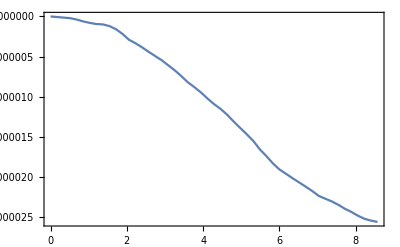

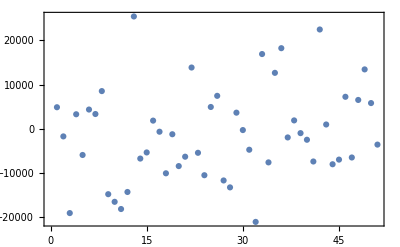

```mathematica
dt=10^-8;tend=1+5 10^-7;
xs=Table[{0,0},{i,1,tend,dt}];
x2s=Table[{0,0},{i,1,tend,dt}];
ws=Table[RandomVariate[NormalDistribution[]]/Sqrt[dt],{i,1,tend,dt}];
m=11 10^-15;γ=6 Pi 0.001 10^-6;temp=300;kb=1.38 10^-23;τ=m/γ
For[t=3,t<tend/dt,t++,
xs[[t]]={t/τ,(2+dt γ/m)/(1+dt γ/m)xs[[t-1,2]]-1/(1+dt γ/m)xs[[t-2,2]]+Sqrt[2 kb temp γ]/(m(1+dt γ/m))dt^(3/2)ws[[t]]};
x2s[[t]]={t/τ,x2s[[t-1,2]]+Sqrt[2 kb temp γ dt]ws[[t]]}
]//Quiet
ListPlot[5 10^7 #&/@x2s,PlotRange->All,Frame->True,Axes->False,Joined->True]
ListPlot[Drop[xs,-1],PlotRange->All,Frame->True,Axes->False,Joined->True]
ListPlot[ws,PlotRange->All,Frame->True,Axes->False]
```